```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory["/Users/brycemorsky/Desktop/New projects/Norms and pandemics/figures"];
SetOptions[{Plot,ParametricPlot,ListPlot,ListLinePlot,ListPlot3D},PlotTheme->"Vibrant",BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->Thickness[0.008]];
```

```mathematica
β=0.41;
δ=0.2;
γ=0.1;
ϵ=1;
g[p_]=1-m*p;
c1=c;
c2=1;
θ=1;
Δu[i_,p_] = -θ*p-c1*m*i+c2;
Δu[i_,p_] = -θ*p-c1*m*(1-m*p)*i+c2 ;
Δu[i_,p_] = -θ*p-c1*(g[0]^0.5-g[1]^0.5)*g[p]^0.5*i+c2;
(* A couple different utility differences (between obeying or disobeying the norm. *)
(* Δu = u(i,1,p)-u(i,0,p) *)
(* Following the notes on Overleaf, here c2=1 *)
eqns={s'[t]==-β*g[p[t]]*s[t]*i[t],e'[t]==β*g[p[t]]*s[t]*i[t]-δ*e[t],i'[t]==δ*e[t]-γ*i[t],p'[t]== ϵ*(1/(1+Exp[100*Δu[i[t],p[t]]])-p[t])};
ics={s[0]==0.99,e[0]==0,i[0]==0.01,p[0]==0};
```

-Graphics3D-

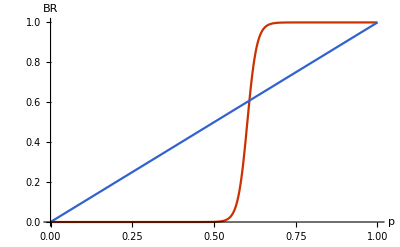

```mathematica
Plot3D[Evaluate[{1/(1+Exp[100*Δu[i,p]]),p}/.{c->20,m->0.8}],{p,0,1},{i,0,1},PlotRange->{{0,1},{0,1}},PlotPoints->100,AxesLabel->{"p","i","BR"}]
Plot[Evaluate[{1/(1+Exp[100*Δu[0.05,p]]),p}/.{c->20,m->0.8}],{p,0,1},PlotPoints->100,AxesLabel->{"p","BR"}]
```

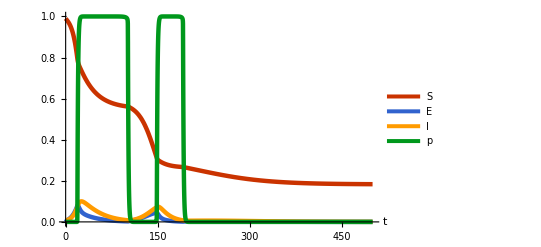

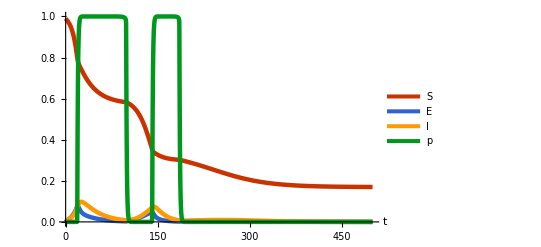

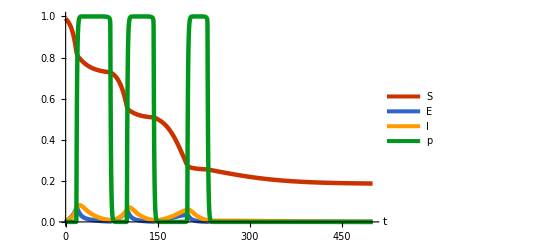

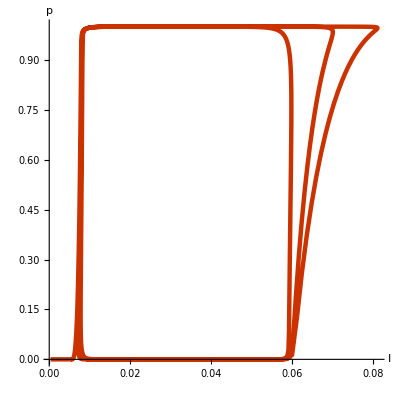

```mathematica
sol=NDSolve[Join[eqns/.{m->0.79,c->25},ics],{s,e,i,p},{t,0,1000}];
plt1=Plot[Evaluate[{s[t],e[t],i[t],p[t]}/.sol],{t,0,500},PlotRange->All,PlotLegends->{"S","E","I","p"},AxesLabel->{"t"}]
sol=NDSolve[Join[eqns/.{m->0.8,c->25},ics],{s,e,i,p},{t,0,1000}];
plt2=Plot[Evaluate[{s[t],e[t],i[t],p[t]}/.sol],{t,0,500},PlotRange->All,PlotLegends->{"S","E","I","p"},AxesLabel->{"t"}]
sol=NDSolve[Join[eqns/.{m->0.88,c->25},ics],{s,e,i,p},{t,0,1000}];
plt3=Plot[Evaluate[{s[t],e[t],i[t],p[t]}/.sol],{t,0,500},PlotRange->All,PlotLegends->{"S","E","I","p"},AxesLabel->{"t"}]
plt4=ParametricPlot[Evaluate[{i[t],p[t]}/.sol],{t,0,500},PlotRange->Full,AspectRatio->1,AxesLabel->{"I","p"}]
Export["plt1.png",plt1,ImageResolution->200];
Export["plt2.png",plt2,ImageResolution->200];
Export["plt3.png",plt3,ImageResolution->200];
Export["plt4.png",plt4,ImageResolution->200];
```

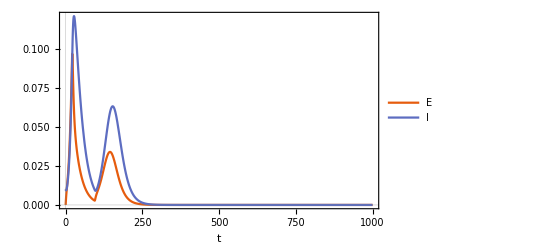

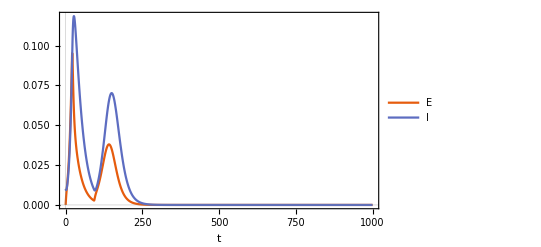

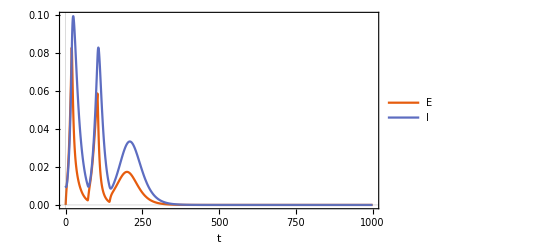

```mathematica
sol=NDSolve[Join[eqns/.{m->0.79,c->20},ics],{e,i},{t,0,1000}];
Plot[Evaluate[{e[t],i[t]}/.sol],{t,0,1000},PlotRange->All,PlotLegends->{"E","I"},AxesLabel->{"t"}]
sol=NDSolve[Join[eqns/.{m->0.8,c->20},ics],{e,i},{t,0,1000}];
Plot[Evaluate[{e[t],i[t]}/.sol],{t,0,1000},PlotRange->All,PlotLegends->{"E","I"},AxesLabel->{"t"}]
sol=NDSolve[Join[eqns/.{m->0.88,c->20},ics],{e,i},{t,0,1000}];
Plot[Evaluate[{e[t],i[t]}/.sol],{t,0,1000},PlotRange->All,PlotLegends->{"E","I"},AxesLabel->{"t"}]
```

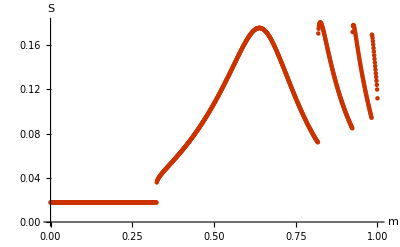

```mathematica
sfin=Array[n,{1001,2}];
count=1;
Do[
sol=NDSolve[Join[eqns/.{m->j/1000,c->20},ics],{s,e,i,p},{t,0,1000}];
sfin[[count]]= Join[{0.001*j},Evaluate[{s[1000]}/.sol][[1]]];
count=count+1;
,{j,0,1000}];
plt5=ListPlot[sfin,PlotStyle->PointSize[0.008],AxesLabel->{"m","S"}]
Export["plt5.png",plt5,ImageResolution->200];
```

```mathematica
sfin=Array[n,{1001*51,3}];
count=1;
Do[
sol=NDSolve[Join[eqns/.{m->j/1000,c->k},ics],{s,e,i,p},{t,0,1000}];
sfin[[count]]= Join[{0.001*j},{k},Evaluate[{s[1000]}/.sol][[1]]];
count=count+1;
,{j,0,1000},{k,0,50}];
plt7 = ListPlot3D[sfin,AxesLabel->{"m","c","S"}]
Export["plt7.png",plt7,ImageResolution->200];
```

-Graphics3D-

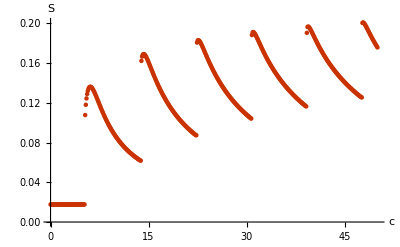

```mathematica
vtheta=Array[n,{501,2}];
count=1;
Do[
sol=NDSolve[Join[eqns/.{m->0.9,c->k/10},ics],{s,e,i,p},{t,0,1000}];
vtheta[[count]]= Join[{0.1*k},Evaluate[{s[1000]}/.sol][[1]]];
count=count+1;
,{k,0,500}];
plt6=ListPlot[vtheta,PlotStyle->PointSize[0.008],AxesLabel->{"c","S"}]
Export["plt6.png",plt6,ImageResolution->200];
```

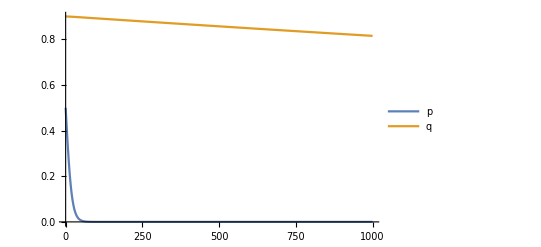

```mathematica
b=2;
c=1;
α=0.9;
ϵ=0.0001;
eqn={p'[t]==p[t]*(1-p[t])*(p[t]*(b-c+α*(1-q[t]))+(1-p[t])*(-c+α*(1-q[t]))-p[t]*(b-α*q[t])-(1-p[t])*(-α*q[t])),q'[t]==ϵ*(p[t]-q[t])};
ic={p[0]==0.5,q[0]== 0.9};
sols=NDSolve[Join[eqn,ic],{p,q},{t,0,1000}];
Plot[Evaluate[{p[t],q[t]}/.sols],{t,0,1000},PlotRange->All,PlotLegends->{"p","q"},AxesLabel->{"t"}]
```

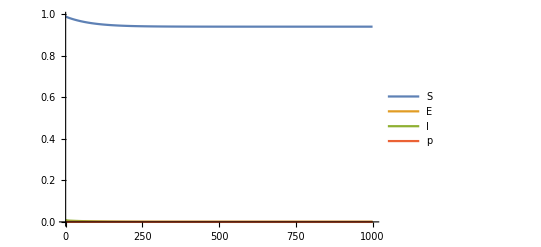

```mathematica
sol=NDSolve[Join[{s'[t]==-β*(1-m)*s[t]*i[t],e'[t]==β*(1-m)*s[t]*i[t]-δ*e[t],i'[t]==δ*e[t]-γ*i[t],p'[t]== ϵ*(1/(1+Exp[-100*(p[t]+θ*i[t]-1)])-p[t])}/.{m->0.79,c->20},ics],{s,e,i,p},{t,0,1000}];
Plot[Evaluate[{s[t],e[t],i[t],p[t]}/.sol],{t,0,1000},PlotRange->All,PlotLegends->{"S","E","I","p"},AxesLabel->{"t"}]
```